```mathematica
Needs["ExperimentEvaluation`"]
SetDirectory["~"];
problemRewrite={"gp.demo.SymbolicRegression"->"1D","gp.demo.SymbolicRegression2D"->"2D","gp.demo.SymbolicRegression3D"->"3D","gp.demo.SymbolicRegression4D"->"4D","gp.demo.Maze"->"M1","gp.demo.MazeRangeFinders"->"M2"};
solverLabelRewrite={"SOLVER",{"GPAT"->"AT","GP"->"G","NEAT"->"N"}};
functionImplRewrite={"gpat.ATFunctions$"->"N","gpat.ATFunctionsNoConsts$"->"NC","gpat.ATFunctionsLikeGP$"->"GP","gpat.ATFunctionsLocks$"->"L"};
functionImplLabelRewrite={"GPAT.FUNCTION_IMPL",functionImplRewrite};
distanceLabelRewrite={"GP.DISTANCE",{"GENERAL"->"G","BASIC"->"I","ISO"->"D","PHENO"->"P","RANDOM"->"R","NODES"->"N","Null"->""}};
distanceGeneralKLabelRewrite={"GP.DISTANCE_GENERAL_K",{}};
distanceGeneralAlphaLabelRewrite={"GP.DISTANCE_GENERAL_DESCEND_NULL_TREES",{"true"->"1","false"->"0"}};
distanceGeneralBetaLabelRewrite={"GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT",{"true"->"1","false"->"0"}};
plotRange={All,{0,100}};
listOfDirectProblems=Grid[{{#[[1]]},{Style[TraditionalForm[#[[2]]],FontSize->12]}}]&/@{{"1D-F",1.5 Subscript[x, 1]^3+2.3 Subscript[x, 1]^2-1.1 Subscript[x, 1]+3.7},{"1D-H",0.1 Subscript[x, 1]^2+0.2Sin[Subscript[x, 1]]},{"2D-I",1.5 Subscript[x, 1] Subscript[x, 2]^2+2.3 Subscript[x, 1] Subscript[x, 2]-1.1 Subscript[x, 2]^2},{"2D-K",Subscript[x, 1] Subscript[x, 2]^2+Subscript[x, 1] Subscript[x, 2]-Subscript[x, 2]^2},{"3D-E",1.5 Subscript[x, 1] Subscript[x, 2]+2.3 Subscript[x, 1]+Subscript[x, 2] Subscript[x, 3]-1.1 Subscript[x, 3]},{"3D-H",1.5 Subscript[x, 1] Subscript[x, 2]^2 Subscript[x, 3]+2.3 Subscript[x, 1] Subscript[x, 2] Subscript[x, 3]-1.1 Subscript[x, 2]+5.3},{"3D-K",Subscript[x, 1] Subscript[x, 2]^2 Subscript[x, 3]-Subscript[x, 1] Subscript[x, 2]+Subscript[x, 2] Subscript[x, 3]},{"4D-C",1.5 Subscript[x, 1] Subscript[x, 2] Subscript[x, 3] Subscript[x, 4]},{"4D-F",1.5 Subscript[x, 1] Subscript[x, 2] Subscript[x, 3]+2.3 Subscript[x, 1]-1.1 Subscript[x, 2]-1.1 Subscript[x, 4]},{"4D-G",1.5 Subscript[x, 1] Subscript[x, 2]^2 Subscript[x, 3] Subscript[x, 4]+2.3 Subscript[x, 1]-1.1 Subscript[x, 2]},{"4D-V",Exp[-1.36709 Subscript[x, 2]^2] Subscript[x, 1](2.43454 Exp[-Subscript[x, 3]^2] -0.393788 Sin[1-Subscript[x, 1]])},{"MAZE-1",""},{"MAZE-2",""}};
listOfDirectProblems={"1D-F","1D-H","2D-I","2D-K","3D-E","3D-H","3D-K","4D-C","4D-F","4D-G","4D-V","MAZE-1","MAZE-2"};
listOfIndirectProblems={"Bit Reverse","Bit Shift","Bit Rotate","Parity","Visual Discrimination","Mobile Robot Navigation"};
```

```mathematica
a=48;
b=44.5;
all=200;
testFisherExact[{{0.01a all,all-0.01a all},{0.01b all,all-0.01b all}}]
```

0.547433

## Experiments Direct

```mathematica
names={"GP","NEAT_GECCO","AT_G_OR","AT_R"};
data=readAllFiles[names,Null,ReplaceParamValues->{}];
```

```mathematica
data=data/.Join[functionImplRewrite,problemRewrite,{"FC55"->"V","FIND_CLUSTER"->"FC"}];
epilog={Text[Style[Grid[{{""},{"K"},{"α"},{"β"}},Spacings->{2,0},Alignment->{Right,Center}],Bold,FontSize->15],{0.0,-14}]};
changingParameters[data]
padding={{15,0},{80,25}};
sortedData = sortDataByParams[data,{"PROBLEM","SYMBOLIC_REGRESSION.F","RECO.GENERATOR","GP.DISTANCE",
"GP.DISTANCE_GENERAL_DESCEND_NULL_TREES","GP.DISTANCE_GENERAL_K","GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT","SOLVER"}];
sortedData = sortDataByParams[data,{"PROBLEM","SYMBOLIC_REGRESSION.F","RECO.GENERATOR","GP.DISTANCE",
"GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT","GP.DISTANCE_GENERAL_K","GP.DISTANCE_GENERAL_DESCEND_NULL_TREES","SOLVER"}];
newLabels=extractParameters[sortedData,{
{"SOLVER",{}},
distanceGeneralKLabelRewrite,
distanceGeneralAlphaLabelRewrite,
distanceGeneralBetaLabelRewrite
}];
newLabels=newLabels/.{{"GP","Null","Null","Null"}->{"G"},{"NEAT","Null","Null","Null"}->{"N"},{"GPAT",none:__}->{"A",none}};
newLabels=newLabels/.{{"A","Null","Null","Null"}->{"R"}};
sortedData=replaceLabels[sortedData,newLabels];
printAsTable[sortedData,{"SOLVER","ID","GPAT.DISTANCE","GPAT.FUNCTION_IMPL","RECO.GENERATOR","PROBLEM","GPAT.DISTANCE_CACT","SYMBOLIC_REGRESSION.F","GP.DISTANCE_GENERAL_DESCEND_NULL_TREES","GP.DISTANCE_GENERAL_K","GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT","MAZE.MAP"}];
```

{GPAT.DISTANCE,GPAT.DISTANCE_CACT,GPAT.DISTANCE_PHENO_HIGH,GPAT.DISTANCE_PHENO_LOW,GPAT.DISTANCE_PHENO_STEPS,GPAT.FUNCTION_IMPL,GP.DISTANCE_GENERAL_DESCEND_NULL_TREES,GP.DISTANCE_GENERAL_K,GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT,GP.MAX_EVALUATIONS,GP.MUTATION_CAUCHY_PROBABILITY,GP.TARGET_FITNESS,GP.TYPE,ID,MAZE.MAP,PARALLEL.FORCE_THREADS,PROBLEM,SOLVER,SYMBOLIC_REGRESSION.F}

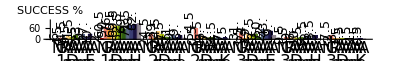

```mathematica
parts = 11;
selectedData=selectData[sortedData,{"PROBLEM"->{"1D","2D","3D"}}];
selectedData=removeData[selectedData,{"GP.DISTANCE_GENERAL_K"->{10.},"GPAT.FUNCTION_IMPL"->{"NC","GP"},"SYMBOLIC_REGRESSION.F"->{"J"}}];
selectedData = Flatten[Permute[#,{3,1,2}]&/@Partition[selectedData,parts],1];
plotBooleanAsBarChartPub[selectedData,"SUCCESS",listOfDirectProblems,2.0,parts,PlotRange->plotRange,Epilog->epilog, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2]
Export["soco2012_1d_2d_3d.eps",%];
```

```mathematica
saveData[selectedData,"DIRECT1"];
```

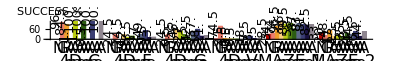

```mathematica
parts = 11;
selectedData=selectData[sortedData,{"PROBLEM"->{"4D","M1","M2"}}];
selectedData=removeData[selectedData,{"GP.DISTANCE_GENERAL_K"->{10.},"GPAT.FUNCTION_IMPL"->{"NC","GP"},"SYMBOLIC_REGRESSION.F"->{"J"}}];
selectedData = Flatten[Permute[#,{3,1,2}]&/@Partition[selectedData,parts],1];
plotBooleanAsBarChartPub[selectedData,"SUCCESS",listOfDirectProblems[[8;;-1]],2.0,parts,PlotRange->plotRange,Epilog->epilog, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2]
Export["soco2012_4d_maze.eps",%];
```

```mathematica
saveData[selectedData,"DIRECT2"];
```

## Experiments Indirect

```mathematica
names={"HGP","HNEAT_GECCO","HAT_G_OR","HAT_R","HGP_robo_GP_GECCO","HNEAT_robo_NEAT_GECCO","HAT_G_ROBO","HAT_R_ROBO"};
data=readAllFiles[names,Null,ReplaceParamValues->{}];
```

```mathematica
data=data/.Join[functionImplRewrite,problemRewrite,{"FC55"->"V","FIND_CLUSTER"->"FC"}];
epilog={Text[Style[Grid[{{""},{"K"},{"α"},{"β"}},Spacings->{2,0},Alignment->{Right,Center}],Bold,FontSize->15],{0.0,-14}]};
changingParameters[data]
padding={{15,0},{80,25}};
sortedData = sortDataByParams[data,{"PROBLEM","RECO.GENERATOR","SOLVER","GP.DISTANCE_GENERAL_DESCEND_NULL_TREES","GP.DISTANCE_GENERAL_K","GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT"}];
sortedData = sortDataByParams[data,{"PROBLEM","RECO.GENERATOR","SOLVER","GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT" ,"GP.DISTANCE_GENERAL_K","GP.DISTANCE_GENERAL_DESCEND_NULL_TREES"}];
newLabels=extractParameters[sortedData,{
{"SOLVER",{}},
distanceGeneralKLabelRewrite,
distanceGeneralAlphaLabelRewrite,
distanceGeneralBetaLabelRewrite
}];
newLabels=newLabels/.{{"GP","Null","Null","Null"}->{"G"},{"NEAT","Null","Null","Null"}->{"N"},{"GPAT",x:__}->{"A",x}};
newLabels=newLabels/.{{"A","Null","Null","Null"}->{"R"}};
sortedData=replaceLabels[sortedData,newLabels];
printAsTable[sortedData,{"SOLVER","ID","GPAT.DISTANCE","GPAT.FUNCTION_IMPL","RECO.GENERATOR","PROBLEM","GPAT.DISTANCE_CACT","SYMBOLIC_REGRESSION.F","GP.DISTANCE_GENERAL_DESCEND_NULL_TREES","GP.DISTANCE_GENERAL_K","GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT","MAZE.MAP"}];
```

{BUILDER,EXPERIMENTS,GPAT.DISTANCE,GPAT.DISTANCE_CACT,GPAT.DISTANCE_PHENO_HIGH,GPAT.DISTANCE_PHENO_LOW,GPAT.DISTANCE_PHENO_STEPS,GPAT.FUNCTION_IMPL,GP.DISTANCE_GENERAL_DESCEND_NULL_TREES,GP.DISTANCE_GENERAL_K,GP.DISTANCE_GENERAL_NOT_MATCHING_NODE_EXIT,GP.MAX_EVALUATIONS,GP.MAX_GENERATIONS,GP.MUTATION_CAUCHY_PROBABILITY,GP.MUTATION_SUBTREE_PROBABLITY,GP.TARGET_FITNESS,GP.TYPE,ID,NEAT.maxGenerations,NET_ACTIVATIONS,PARALLEL.FORCE_THREADS,PRINT.finished,PRINT.finishedShowHyperNet,PRINT.finishedShowProblem,PRINT.generation,PRINT.progress,PRINT.progressShowHyperNet,PRINT.progressShowProblem,PRINT.storeRun,PROBLEM,RECO.GENERATOR,RECO.LINE_SIZE,SOLVER}

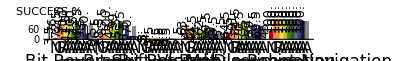

```mathematica
parts = 11;
selectedData=removeData[sortedData,{"GP.DISTANCE_GENERAL_K"->{10.},"GPAT.FUNCTION_IMPL"->{"NC","GP"},"SYMBOLIC_REGRESSION.F"->{"J"}}];
selectedData = Flatten[Permute[#,{11,1,2,3,4,5,6,7,8,9,10}]&/@Partition[selectedData,parts],1];
selectedData = Flatten[Permute[Partition[selectedData,parts],{2,4,3,6,1,5}],1];
plotBooleanAsBarChartPub[selectedData,"SUCCESS",listOfIndirectProblems,2.0,parts,PlotRange->plotRange,Epilog->epilog, ImagePadding->padding,AspectRatio->0.25/GoldenRatio,ImageSize->{{1400},{3200}},BarLabelsRotate->Pi/2]
Export["soco2012_indirect.eps",%];
```

```mathematica
saveData[selectedData,"INDIRECT"];
```